# Nematic fluids of discs mixed with shape-persistent living polymers

## Initialization

```mathematica
Clear["Global`*"]
```

Define some fixed parameters:

```mathematica
(*eb=1;
qq = (1+√(1+4*4*Exp[-eb]))/2;
zz = ((1+√(1+4*4*Exp[-eb]))/2)^2;*)
qq=1;
zz=1;
precision=20;
```

Definition of functions:

```mathematica
(* alignment amplitudes *)

ar[rr0_, rd0_, srav_, sd_]:=(5/4)*(rr0*srav-2*qq*rd0*sd);
ad[rr0_, rd0_, srav_, sd_]:=(5/4)*(zz*rd0*sd-2*qq*rr0*srav);

(* chi parameter for weakly flexible  rods *)

xi[lp_, rr0_, rd0_, srav_, sd_]:=1+Abs[ar[rr0, rd0, srav, sd]]+lp-√(1+2*lp+2*Abs[ar[rr0, rd0, srav, sd]]*lp+lp^2);
(* effective amplitude *)

arbar[lp_, rr0_, rd0_, srav_, sd_]:=ar[rr0, rd0, srav, sd]-Sign[ar[rr0, rd0, srav, sd]]*xi[lp, rr0, rd0, srav, sd];
(* polymer length distribution *)
rln[lp_, eb_, rr0_, rd0_, srav_, sd_, lambda_, ll_]:=ll*Exp[SetPrecision[eb+lambda*ll,precision]]*Exp[SetPrecision[arbar[lp, rr0, rd0, srav, sd]*ll,precision]]*DawsonF[SetPrecision[√((3*arbar[lp, rr0, rd0, srav, sd]*ll)/2),precision]]/(√((3*arbar[lp, rr0, rd0, srav, sd]*ll)/2));
(* nematic order parameters *)
srl[lp_, rr0_, rd0_, srav_, sd_, ll_]:=1/4 (-2-2/(arbar[lp, rr0, rd0, srav, sd]*ll)+(√6)/(√(arbar[lp, rr0, rd0, srav, sd]*ll) DawsonF[SetPrecision[√((3*arbar[lp, rr0, rd0, srav, sd]*ll)/2),precision]]));
sdf[rr0_, rd0_, srav_, sd_]:=1/4 (-2-2/ad[rr0, rd0, srav, sd]+(√6)/(√ad[ rr0, rd0, srav, sd] DawsonF[SetPrecision[√((3*ad[rr0, rd0, srav, sd])/2),precision]]));
```

## Initialization (v2)

```mathematica
Clear["Global`*"]
```

Define some fixed parameters:

```mathematica
(*eb=1;
qq = (1+√(1+4*4*Exp[-eb]))/2;
zz = ((1+√(1+4*4*Exp[-eb]))/2)^2;*)
qq=1;
zz=1;
precision=100;
llmax=150;
```

Definition of functions:

```mathematica
(* alignment amplitudes *)

ar=(5/4)*(rrn*srav-2*qq*rdn*sd);
ad=(5/4)*(zz*rdn*sd-2*qq*rrn*srav);

(* chi parameter for weakly flexible  rods *)

xi=1+Abs[ar]+lp-√(1+2*lp+2*Abs[ar]*lp+lp^2);
(* effective amplitude *)

arbar=ar-Sign[ar]*xi;
(* polymer length distribution *)
rln[ll_]:=ll*Exp[SetPrecision[eb+lambda*ll,precision]]*Exp[SetPrecision[arbar*ll,precision]]*DawsonF[SetPrecision[√((3*arbar*ll)/2),precision]]/(√((3*arbar*ll)/2));
(* nematic order parameters *)
srl[ll_]:=1/4 (-2-2/(arbar*ll)+(√6)/(√(arbar*ll) DawsonF[SetPrecision[√((3*arbar*ll)/2),precision]]));
sdf:=1/4 (-2-2/ad+(√6)/(√ad DawsonF[SetPrecision[√((3*ad)/2),precision]]));
```

## Polymer Distributions in the Nematic Phase

Equation system to obtain OverBar[S_r], S_d and λ:

```mathematica
normalization[lp_, eb_, rr0_, rd0_, srav_, sd_, lambda_]:=(ll = 1;sum = 0; rl = rln[lp, eb, rr0, rd0, srav, sd, lambda, ll];
While[rl>10^-5, 
sum = sum + rl;
ll=ll+1; 
rl = rln[lp, eb, rr0, rd0, srav, sd, lambda, ll]
];
sum);
order[lp_, eb_, rr0_, rd0_, srav_, sd_, lambda_]:=(ll = 1;
sum = 0; rl = rln[lp, eb, rr0, rd0, srav, sd, lambda, ll];
While[rl>10^-5, 
sum = sum + srl[lp, rr0, rd0, srav, sd, ll]*rl; 
ll =ll+1; 
rl = rln[lp, eb, rr0, rd0, srav, sd, lambda, ll]
];
rr0^-1*sum);
solveConditions[lp_, eb_,rr0_,rd0_,llmax_, sravs_, sds_, lambdas_]:=FindRoot[{
normalization[lp, eb, rr0, rd0, srav, sd, lambda]==rr0,
order[lp, eb, rr0, rd0, srav, sd, lambda]==srav,
sdf[rr0,rd0,srav,sd]==sd
},{{lambda,lambdas},{srav,sravs,-1,1},{sd,sds,-1,1}}];
```

### Plot

```mathematica
lp=5;
(*eb=1;*)
xx=0.1;
cc=4;
llmax=150;
sravs=0.5;
sds=-0.7;
lambdas=-3;
rr0=cc*(1-xx);
rd0=cc*xx;
order[lp, eb, rr0, rd0, sravs, sds, lambdas]
solv1 = {lambda,srav, sd}/.solveConditions[lp, eb, rr0, rd0, llmax, sravs, sds, lambdas];
lambdan=Re[solv1[[1]]]
sravn=Re[solv1[[2]]]
sdn=Re[solv1[[3]]]
Plot[rln[lp, eb, rr0, rd0, sravn, sdn, lambdan, ll], {ll,1,llmax}, PlotRange->Full]
```

```mathematica
(*TODO: save interesting data to files, for a better representation*)
```

## Polymer Distributions in the Nematic Phase (v2)

Equation system to obtain OverBar[S_r], S_d and λ:

```mathematica
solveConditions[lp_, eb_,rrn_,rdn_,llmax_, sravs_, sds_, lambdas_]:=FindRoot[{
Sum[rln[ll],{ll,1,llmax}]==rrn,
rrn^-1*Sum[srl[ll]*rln[ll],{ll,1,llmax}]==srav,
sdf==sd
},{{lambda,lambdas},{srav,sravs,-1,1},{sd,sds,-1,1}}];
```

### Plot

-3.12044

0.917428

-0.44102

3.0385

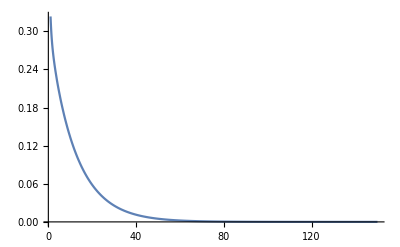

```mathematica
lp=5;
eb=1;
xx=0.1;
cc=4;
llmax=150;
sravs=0.7;
sds=-0.4;
lambdas=-2;
rrn=cc*(1-xx);
rdn=cc*xx;
solv1 = {lambda,srav, sd}/.solveConditions[lp, eb, rrn, rdn, llmax, sravs, sds, lambdas];
lambda=Re[solv1[[1]]]
srav=Re[solv1[[2]]]
sd=Re[solv1[[3]]]
arbar
Plot[rln[ll], {ll,1,llmax}, PlotRange->Full]
```

```mathematica
(*TODO: save interesting data to files, for a better representation*)
```

### Parameter interpolations in terms of the concentration

```mathematica
lp=5;
eb=1;
llmax=150;
sravs=0.8;
sds=-0.4;
lambdas=-3;
xx=0.1;
lambdad={};
sravd={};
sdd={};
For[cc=1,cc<4.3,cc=cc+0.4;
rr0=cc*(1-xx);
rd0=cc*xx;
solv1 = {lambda,srav, sd}/.solveConditions[lp, eb, rr0, rd0, llmax, sravs, sds, lambdas];
lambdan=Re[solv1[[1]]];
sravn=Re[solv1[[2]]];
sdn=Re[solv1[[3]]];
AppendTo[lambdad,{cc,lambdan}];
AppendTo[sravd,{cc,sravn}];
AppendTo[sdd,{cc,sdn}];
Print[cc, " ", lambdan, " ", sravn, " ", sdn];
(*sravs=sravn;
sds=sdn;
lambdas=lambdan;*)

];
lambdaInterp=Interpolation[lambdad];
sravInterp=Interpolation[sravd];
sdInterp=Interpolation[sdd];
```

1.4 -1.36124 1.62302×10^-8 -2.13533×10^-8

1.8 -1.21855 2.98658×10^-8 -2.43009×10^-8

2.2 -1.49712 0.509162 -0.316854

2.6 -1.96419 0.733749 -0.387269

3. -2.33327 0.824722 -0.412666

3.4 -2.66456 0.874918 -0.427278

3.8 -2.97279 0.906071 -0.437145

4.2 -3.26451 0.926834 -0.444395

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

FindRoot::nlnum: The function value {941.238,Indeterminate,0.000120363+0. ⅈ} is not a list of numbers with dimensions {3} at {lambda,srav,sd} = {-3.29402,0.88548,-0.447052}.

4.6 -3.16886 0.844231 -0.444477

## Isotropic-Nematic phase transition

Functions for the chemical potential and the pressure:

```mathematica
wur[ll_]:=-3/2*((arbar*ll)^2+2*arbar*ll)*srl[ll];

wud[ll_]:=3/4*(arbar*ll)^2+(3/2*(arbar*ll)^2-3*arbar*ll)*srl[ll];

sigmarod[ll_]:=-Log[Exp[SetPrecision[arbar*ll,precision]]*DawsonF[SetPrecision[√((3*arbar*ll)/2),precision]]/(√(3/2*arbar*ll))]+ arbar*ll*srl[ll];

sigmadisk=-Log[Exp[SetPrecision[ad,precision]]*DawsonF[SetPrecision[√((3*ad)/2),precision]]/(√(3/2*ad))]+ad*sd;

rli[ll_]:=ll*Exp[eb]*(1-SetPrecision[2/(1+√(1+4*rri*Exp[-eb])),precision])^ll;

muriso=  2*rri+2*qq*rdi+Sum[rli[ll]/(ll*rri)*(Log[rli[ll]/ll]-eb),{ll, 1,llmax}];

(*murnem [lp_, eb_, rrn_, rdn_, srav_, sd_, lambda_, llmax_]:=2*rrn*(1-5/8*srav^2)+2*qq*rdn*(1+5/4*srav*sd)+Sum[rl[lp, eb, rrn, rdn, srav, sd, lambda, ll]/(ll*rrn)*(Log[rl[lp, eb, rrn, rdn, srav, sd, lambda, ll]/ll]+sigmarod[lp, rrn, rdn, srav, sd,ll]-eb-2*ll/(3*lp)*Which[(rdn/(rrn+rdn))<0.5,wur[lp, rrn, rdn, srav, sd,ll],(rdn/(rrn+rdn))>=0.5,wud[lp, rrn, rdn, srav, sd, ll]]),{ll, 1,llmax}];*)
murnem =2*rrn*(1-5/8*srav^2)+2*qq*rdn*(1+5/4*srav*sd)+Sum[rln[ll]/(ll*rrn)*(Log[rln[ll]/ll]+sigmarod[ll]-eb-2*ll/(3*lp)*wur[ll]),{ll, 1,llmax}];

mudiso=Log[rdi]+2*zz*rdi+2*qq*rri;

mudnem=Log[rdn]+sigmadisk+2*zz*rdn*(1-5/8*sd^2)+2*qq*rrn*(1+5/4*srav*sd);

pressureiso=Sum[rli[ll]/ll,{ll,1,llmax}]+rdi+rri^2+2*qq*rri*rdi+zz*rdi^2;

pressurenem=Sum[rln[ll]/ll,{ll,1,llmax}]+rdn+rrn^2*(1-5/8 srav^2)+2*qq*rrn*rdn*(1+5/4*srav*sd)+zz*rdn^2*(1-5/8*sd^2);
```

Equation system to obtain OverBar[S_r], S_d, λ, c_i, c_n, x_n:

```mathematica
solveConditions2[lp_, eb_,llmax_, sravs_, sds_, lambdas_, rri_, rrns_, rdis_, rdns_]:=(n=0;
FindRoot[{
Sum[rln[ll],{ll,1,llmax}]==rrn,
rrn^-1*Sum[srl[ll]*rln[ll],{ll,1,llmax}]==srav,
sdf==sd,
muriso==murnem,
mudiso==mudnem,
pressureiso==pressurenem

},{{lambda,lambdas},{srav,sravs,-1,1},{sd,sds,-1,1}, {rrn, rrns,10^-10,15}, {rdi,rdis,10^-10,15}, {rdn,rdns,10^-10,15}},EvaluationMonitor:>(n++;Print[{n}])]);
(*{{lambda,lambdas},{srav,sravs},{sd,sds}, {rrn, rrns}, {rdi,rdis}, {rdn,rdns}},EvaluationMonitor:>(n++;Print[{n}])*)
pressure [lp_, eb_,llmax_, sravs_, sds_, lambdas_, xxns_, ccis_, ccns_, xxi_]:= (
rri=ccis*(1-xxi);
rdis=ccis*xxi;
rrns=ccns*(1-xxns);
rdns=ccns*xxns;
solv2 = {lambda,srav, sd, rrn,rdi,rdn}/.solveConditions2[lp, eb, llmax, sravs, sds, lambdas, rri, rrns, rdis, rdns];
lambda=Re[solv2[[1]]];
srav=Re[solv2[[2]]];
sd=Re[solv2[[3]]];
rrn=Re[solv2[[4]]];
rdi=Re[solv2[[5]]];
rdn=Re[solv2[[6]]];
xxnn=rdn/(rrn+rdn);
ccin=rri+rdi;
ccnn=rrn+rdn;
{xxi, pressureiso,xxnn,pressurenem,lambda, srav,sd,ccin,ccnn}
)
```

### Plot

```mathematica
lp=5;
eb=-1;
llmax=150;
sravs=0.5;
sds=-0.5;
lambdas=-2;
xxi=0.2;
xxns=0.2;
ccis=3.2;
ccns=3.2;
(*Plot[pressure [lp, eb,llmax, sravs, sds, lambdas, xxns, ccis, ccns, xxi][[2]], {xxi,0.01,0.99},PlotPoints->4, PlotRange->Full]*)
pressure[lp, eb,llmax, sravs, sds, lambdas, xxns, ccis, ccns, xxi]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{0.2,6.88669,9.52808×10^-6,4.71826,-1.2419,0.45498,-0.441412,2.56002,2.32023}

#### Limit situations

x = 0 -> Pure rods

```mathematica
rdi=0;
rdn=0;
sd=0;
lp=5;
eb=1;
sravs=0.5;
lambdas=-2.5;
ccis=1;
ccns=2;
solveConditions4[lp_, eb_,sravs_, lambdas_, rris_, rrns_]:=(n=0;
FindRoot[{
-(ⅇ^eb (√3 √arbar (arbar-2 lambda)+2 (-arbar-lambda)^(3/2) √(2-(3 arbar)/(arbar+lambda)) ArcSinh[(√(3/2) √arbar)/(√(-arbar-lambda))]))/(√3 √arbar (arbar-2 lambda)^2 (arbar+lambda))==rrn,
rrn^-1*(ⅇ^eb (-3 √arbar lambda+(2 √3 √(-arbar-lambda) (-arbar+lambda) ArcSinh[(√(3/2) √arbar)/(√(-arbar-lambda))])/(√(2-(3 arbar)/(arbar+lambda)))))/(3 arbar^(3/2) (arbar-2 lambda) (arbar+lambda))==srav,
muriso==murnem,
pressureiso==pressurenem

},{{lambda,lambdas},{srav,sravs,-1,1},{rri, rris,10^-10,15}, {rrn,rrns,10^-10,15}},EvaluationMonitor:>(n++;Print[{n, sd, lambda, srav, rri, rrn}])]);
rris=ccis;
rrns=ccns;
solv2 = {lambda,srav, rri, rrn}/.solveConditions4[lp, eb, sravs,lambdas, rris, rrns]
lambda=Re[solv2[[1]]];
srav=Re[solv2[[2]]];
rri=Re[solv2[[3]]];
rrn=Re[solv2[[4]]];
ccin=rri;
ccnn=rrn;
{0, pressureiso,0,pressurenem,lambda, srav,ccin,ccnn}
Clear[lambda,srav,rri,rrn]
```

{-1.21563,-6.79318×10^-9,1.62875,1.62875}

{0,3.79861,0,3.79861+0. ⅈ,-1.21563,-6.79318×10^-9,1.62875,1.62875}

x = 1 -> Pure disks

```mathematica
rri=0;
rrn=0;
srav=0;
pressureiso=rdi+rri^2+2*qq*rri*rdi+zz*rdi^2;

pressurenem=rdn+rrn^2*(1-5/8 srav^2)+2*qq*rrn*rdn*(1+5/4*srav*sd)+zz*rdn^2*(1-5/8*sd^2);
lp=5;
eb=1;
sds=0.8;
ccis=6;
ccns=3;
solveConditions5[lp_, eb_,sds_, rdis_, rdns_]:=(n=0;
FindRoot[{
sdf==sd,
mudiso==mudnem,
pressureiso==pressurenem

},{{sd,sds,-1,1},{rdi, rdis,10^-10,15}, {rdn,rdns,10^-10,15}},EvaluationMonitor:>(n++;Print[{n, srav, sd, rdi, rdn}])]);
rdis=ccis;
rdns=ccns;
solv2 = {sd, rdi, rdn}/.solveConditions5[lp, eb, sds,rdis, rdns]
sd=Re[solv2[[1]]];
rdi=Re[solv2[[2]]];
rdn=Re[solv2[[3]]];
ccin=rdi;
ccnn=rdn;
{0, pressureiso,0,pressurenem,sd,ccin,ccnn}
Clear[sd,rdi,rdn]
```

{0.57351,3.50438,3.87238}

{0,15.7851,0,15.7851,0.57351,3.50438,3.87238}

## Draft/Tests

### With the While-Loop:

```mathematica
solveConditions3[lp_, eb_,llmax_, srav_, sd_, lambda_, rri_, rrns_, rdis_, rdns_]:=FindRoot[{

muriso[eb, rri, rdi, llmax]==murnem[lp, eb, rrn, rdn, srav, sd, lambda, llmax],
mudiso[rri,rdi]==mudnem[lp,rrn, rdn, srav, sd],
pressureiso[eb, rri,rdi, llmax]==pressurenem[lp, eb, rrn, rdn, srav, sd, lambda, llmax]

},{{rrn, rrns,10^-5,10}, {rdi,rdis,10^-5,10}, {rdn,rdns,10^-5,10}}];
```

```mathematica
lp=5;
eb=1;
llmax=150;
sravs=0.8624569216635748;
sds=-0.40577124411248866;
lambdas=-2.9689877260665503;
xxi=0.1;
xxns=0.01;
ccis=3.6029484239166867;
ccns=3.9801539278678573;
rri=ccis*(1-xxi);
rdis=ccis*xxi;
rrns=ccns*(1-xxns);
rdns=ccns*xxns;
df=100;

While[df>1,
solv2 = {lambda,srav, sd}/.solveConditions[lp, eb,rrns,rdns,llmax, sravs, sds, lambdas];
lambdan=Re[solv2[[1]]];
sravn=Re[solv2[[2]]];
sdn=Re[solv2[[3]]];
Print[lambdan, sravn, sdn];

solv3 = {rrn,rdi,rdn}/.solveConditions3[lp, eb,llmax, sravn, sdn, lambdan, rri, rrns, rdis, rdns];
rrnn=Re[solv3[[1]]];
rdin=Re[solv3[[2]]];
rdnn=Re[solv3[[3]]];
df=10^5*Max[{Abs[sravs-sravn],Abs[sds-sdn],Abs[lambdas-lambdan],Abs[rdis-rdin],Abs[rrns-rrnn],Abs[rdns-rdnn]}];
sravs=sravn;
sds=sdn;
lambdas=lambdan;
rdis=rdin;
rrns=rrnn;
rdns=rdnn;
Print[df]
];
xxnn=rdnn/(rrnn+rdnn);
ccin=rri+rdin;
ccnn=rrnn+rdnn;
{xxi, pressureiso[eb, rri,rdin, llmax],xxnn,pressurenem[lp, eb, rrnn, rdnn, sravn, sdn, lambdan, llmax]}
{lambdan, sravn, sdn, xxnn, ccin, ccnn}
```

-3.124310.922809-0.445131

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

359907.

-2.288834.1716×10^-8-2.29122×10^-8

FindRoot::reged: The point {0.931136+0. ⅈ,7.71567+0. ⅈ,10.+0. ⅈ} is at the edge of the search region {0.00001,10.} in coordinate 3 and the computed search direction points outside the region.

748833.

-1.549023.04969×10^-9-8.57716×10^-10

FindRoot::reged: The point {0.931136,7.71567,10.} is at the edge of the search region {0.00001,10.} in coordinate 3 and the computed search direction points outside the region.

73981.1

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-1.549023.04968×10^-9-8.57716×10^-10

FindRoot::reged: The point {0.931136,7.71567,10.} is at the edge of the search region {0.00001,10.} in coordinate 3 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

3.18084×10^-10

{0.1,129.707,0.914818,130.223}

{-1.54902,3.04968×10^-9,-8.57716×10^-10,0.914818,10.9583,10.9311}

### Others

```mathematica
Integrate[Exp[a*x^2]*Sin[x], {x, 0, Pi}]
```

(ⅇ^(1/4/a) √π (-2 Erf[1/(2 √a)]+Erf[(1-2 ⅈ a π)/(2 √a)]+Erf[(1+2 ⅈ a π)/(2 √a)]))/(4 √a)

```mathematica
DawsonF[√((3*arbar[5, 3, 3, 0.8, -0.3]*143)/2)]
```

General::munfl: Exp[-730.897] is too small to represent as a normalized machine number; precision may be lost.

0.0185071

```mathematica
DawsonF[SetPrecision[√((3*arbar[5, 3, 3, 0.8, -0.3]*143)/2),20]]
```

0.01850715269772228

```mathematica
(1.000000082740371*^-10)^-1*Sum[srl[5,1.000000082740371*^-10, 6.403333933053428, 0.8635690936310091, -0.327170864745854, ll]*rl[5, 1, 1.000000082740371*^-10, 6.403333933053428, 0.8635690936310091, -0.327170864745854, -4.765905785346516, ll],{ll,1,150}]
```

7.23822×10^8

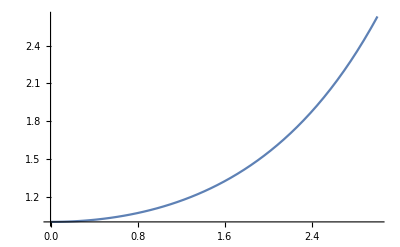

```mathematica
s=Exp[x]*DawsonF[√((3*x)/2)]/√((3*x)/2);
Plot[s,{x,0,3}]
```

```mathematica
(2/(1+√(1+4*4*Exp[-1])))^-1
```

1/2 (1+√(1+16/ⅇ))

```mathematica
N[1/2 (1+√(1+16/ⅇ))]
```

1.81207

```mathematica
(*Subscript[ϵ, b]=1;
λ = -2.7;
α = 2.6;*)
y[x_]=1/(2x)+1/(4 x^3)+3/(8 x^5)
∑_(l=1)^∞ l*ⅇ^(eb+l*λ)ⅇ^(α*l)y[√((3α*l)/2)]/(√((3α*l)/2))
```

3/(8 x^5)+1/(4 x^3)+1/(2 x)

-(ⅇ^eb (3 ⅇ^(α+λ) α^2-α Log[1-ⅇ^(α+λ)]+ⅇ^(α+λ) α Log[1-ⅇ^(α+λ)]+PolyLog[2,ⅇ^(α+λ)]-ⅇ^(α+λ) PolyLog[2,ⅇ^(α+λ)]))/(9 (-1+ⅇ^(α+λ)) α^3)

```mathematica
∑_(l=1)^∞ l*ⅇ^eb(1-2/(1+√(1+4*Subscript[ρ, r]*Exp[-eb])))^l
```

ρ_r

```mathematica
Subscript[ϵ, b]=1;
λ = -2.7;
α = 2.6;
Plot[l*ⅇ^(Subscript[ϵ, b]+l*λ)ⅇ^(α*l)DawsonF[√((3α*l)/2)]/(√((3α*l)/2)), {l,1,50}]
```

```mathematica
(* Dawson function approximation:
http://www.scielo.org.mx/scielo.php?script=sci_arttext&pid=S0188-62662019000100175&lng=es&nrm=iso*)
```

```mathematica
∫_0^∞ l*ⅇ^(eb+l*λ)ⅇ^(α*l)DawsonF[√((3α*l)/2)]/(√((3α*l)/2))ⅆl
```

ConditionalExpression[-(ⅇ^eb (√3 √α (α-2 λ)+2 (-α-λ)^(3/2) √(2-(3 α)/(α+λ)) ArcSinh[(√(3/2) √α)/(√(-α-λ))]))/(√3 √α (α-2 λ)^2 (α+λ)), Re[-α/2+λ]<0&&Re[α+λ]<0]

```mathematica
∫_0^∞ 1/4 (-2-2/(α*l)+(√6)/(√(α*l)* DawsonF[√((3*α*l)/2)]))*l*ⅇ^(eb+l*λ)ⅇ^(α*l)DawsonF[√((3α*l)/2)]/(√((3α*l)/2))ⅆl
```

ConditionalExpression[-(ⅇ^eb (-3 √α λ+(2 √3 √(-α-λ) (-α+λ) ArcSinh[(√(3/2) √α)/(√(-α-λ))])/(√(2-(3 α)/(α+λ)))))/(3 α^(3/2) (α-2 λ) (α+λ)), Re[-α/2+λ]<0&&Re[α+λ]<0]